## Which group to try and go to?

```mathematica
pMu[gMu_,tNu_]:=If[gMu+tNu>1, 1/(gMu+tNu), 1]
pNu[gNu_,tMu_]:=If[gNu+tMu>1, 1/(gNu+tMu), 1]
```

```mathematica
piMuG[gMu_, gNu_,tMu_,tNu_, piMu_, piNu_]:=pMu[gMu,tNu]*piMu+(1-pMu[gMu,tNu])*piNu
piMuT[gMu_, gNu_,tMu_,tNu_, piMu_, piNu_]:=pNu[gNu,tMu]*piNu+(1-pNu[gNu,tMu])*piMu

piNuG[gMu_, gNu_,tMu_,tNu_, piMu_, piNu_]:=pNu[gNu,tMu]*piNu+(1-pNu[gNu,tMu])*piMu
piNuT[gMu_, gNu_,tMu_,tNu_, piMu_, piNu_]:=pMu[gMu,tNu]*piMu+(1-pMu[gMu,tNu])*piNu
```

```mathematica
piMuG[gMu, gNu,tMu,tNu, piMu, piNu]/.{tMu->1-gMu, tNu->1-gNu}
```

piNu (1-If[1+gMu-gNu>1,1/(gMu+(1-gNu)),1])+piMu If[1+gMu-gNu>1,1/(gMu+(1-gNu)),1]

#### Only copy your own group...

```mathematica
gMuDot[gMu_, gNu_,tMu_,tNu_, piMu_, piNu_]:=gMu*(piMuG[gMu, gNu,tMu,tNu, piMu, piNu]-(gMu*piMuG[gMu, gNu,tMu,tNu, piMu, piNu]+tMu*piMuT[gMu, gNu,tMu,tNu, piMu, piNu]))
gNuDot[gMu_, gNu_,tMu_,tNu_, piMu_, piNu_]:=gNu*(piNuG[gMu, gNu,tMu,tNu, piMu, piNu]-(gNu*piNuG[gMu, gNu,tMu,tNu, piMu, piNu]+tNu*piNuT[gMu, gNu,tMu,tNu, piMu, piNu]))
```

Check...

```mathematica
gMuDot[gMu, gNu,tMu,tNu, piMu, piNu]/.{tMu->1-gMu, tNu->1-gNu}/.{piMu->3, piNu->1}/.{gMu->0.2, gNu->0.6}
gNuDot[gMu, gNu,tMu,tNu, piMu, piNu]/.{tMu->1-gMu, tNu->1-gNu}/.{piMu->3, piNu->1}/.{gMu->0.2, gNu->0.6}
```

0.228571

-0.342857d

And plot...

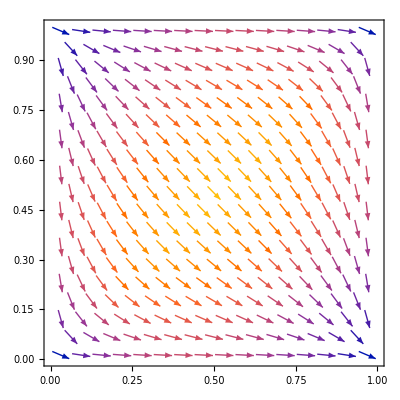

```mathematica
VectorPlot[{gMuDot[gMu, gNu,tMu,tNu, piMu, piNu]/.{tMu->1-gMu, tNu->1-gNu}/.{piMu->3, piNu->1}, gNuDot[gMu, gNu,tMu,tNu, piMu, piNu]/.{tMu->1-gMu, tNu->1-gNu}/.{piMu->3, piNu->1}},{gMu, 0, 1},{gNu, 0, 1}]
```

### Copy the other group...

```mathematica
gMuDot[gMu_, gNu_,tMu_,tNu_, piMu_, piNu_]:=gMu*(piNuG[gMu, gNu,tMu,tNu, piMu, piNu]-(gNu*piNuG[gMu, gNu,tMu,tNu, piMu, piNu]+tNu*piNuT[gMu, gNu,tMu,tNu, piMu, piNu]))
gNuDot[gMu_, gNu_,tMu_,tNu_, piMu_, piNu_]:=gNu*(piMuG[gMu, gNu,tMu,tNu, piMu, piNu]-(gMu*piMuG[gMu, gNu,tMu,tNu, piMu, piNu]+tMu*piMuT[gMu, gNu,tMu,tNu, piMu, piNu]))
```

Check...

```mathematica
gMuDot[gMu, gNu,tMu,tNu, piMu, piNu]/.{tMu->1-gMu, tNu->1-gNu}/.{piMu->3, piNu->1}/.{gMu->0.2, gNu->0.6}
gNuDot[gMu, gNu,tMu,tNu, piMu, piNu]/.{tMu->1-gMu, tNu->1-gNu}/.{piMu->3, piNu->1}/.{gMu->0.2, gNu->0.6}
```

-0.114286

0.685714

And plot...

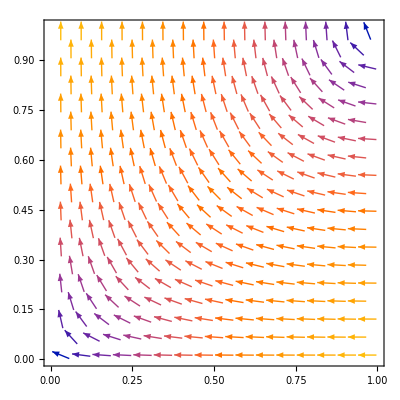

```mathematica
VectorPlot[{gMuDot[gMu, gNu,tMu,tNu, piMu, piNu]/.{tMu->1-gMu, tNu->1-gNu}/.{piMu->3, piNu->1}, gNuDot[gMu, gNu,tMu,tNu, piMu, piNu]/.{tMu->1-gMu, tNu->1-gNu}/.{piMu->3, piNu->1}},{gMu, 0, 1},{gNu, 0, 1}]
```